# Rb experiment magnetic fields

```mathematica
μ0 = 4π *10^-7;(*m kg s^-2 A^-2*)
```

#### Field from a single loop

```mathematica
Clear[Bρ,Bx,By,Bz]
Bx[x_?NumericQ,z_?NumericQ,R_?NumericQ]:=NIntegrate[(-z R(Sin[ϕ]+Cos[ϕ]))/(((R Cos[ϕ]-x)^2+R^2 Sin[ϕ]^2+z^2)^(3/2)),{ϕ,0,2π},Method->"GlobalAdaptive"];
Bz[x_?NumericQ,z_?NumericQ,R_?NumericQ]:=NIntegrate[(R (x Cos[ϕ]-R))/(((R Cos[ϕ]-x)^2+R^2 Sin[ϕ]^2+z^2)^(3/2)),{ϕ,0,2π},Method->"GlobalAdaptive"];
```

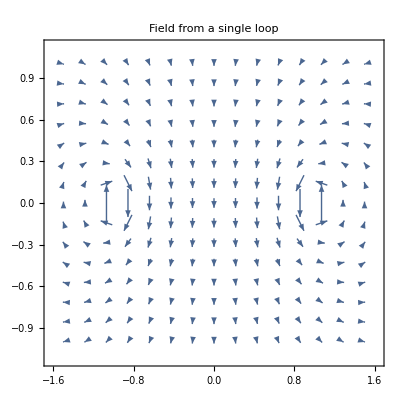

```mathematica
R=1;
VectorPlot[{Bx[x,z,R],Bz[x,z,R]},{x,-1.5,1.5},{z,-1,1},PlotLabel->"Field from a single loop"]
```

#### Quadrupole field

Two loops in an anti-Helmholtz configuration (fields oppose each other).

```mathematica
Clear[loopField,upperLoopField,lowerLoopField,R]
```

```mathematica
Subscript[loopField[x_,z_,R_], z0_,pol_]:={pol*Bx[x,z-z0,R],pol*Bz[x,z-z0,R]} ;
```

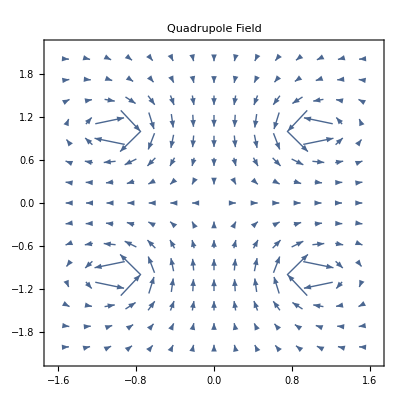

```mathematica
R=1;
VectorPlot[Subscript[loopField[x,z,R], 1,1]+Subscript[loopField[x,z,R], -1,-1],{x,-1.5,1.5},{z,-2,2},PlotLabel->"Quadrupole Field"]
```

Field above, along the quantization axis (axis through center of both coils, z).

```mathematica
loopFieldOnAxis[z_]:=∫_0^(2 π) -R^2/((R^2+z^2)^(3/2))ⅆϕ
```

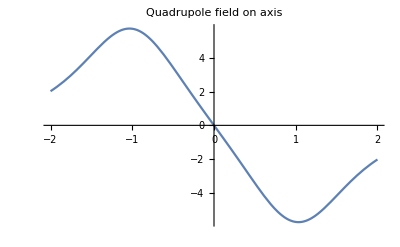

```mathematica
Plot[loopFieldOnAxis[z-1]-loopFieldOnAxis[z+1],{z,-2,2},PlotLabel->"Quadrupole field on axis"]
```

Atoms in the region between the coils, on or near the quantization axis see a force proportional to the gradient of the field.

#### Multi-loop and angled configurations

Try to create a current loop “object” with information about the loop location and maybe a graphic for the loop cross section in xz

```mathematica
Clear[loopField,β]
```

```mathematica
Ry[β_] := {{Cos[β],-Sin[β]},{Sin[β],Cos[β]}};
Ry[-β].{x,z}
```

{x Cos[β]+z Sin[β],z Cos[β]-x Sin[β]}

```mathematica
loopField[x_,z_,R_,x0_,z0_,pol_,β_]:=pol*Ry[β].{Bx[x Cos[β]+z Sin[β]-x0,z Cos[β]-x Sin[β]-z0,R],Bz[x Cos[β]+z Sin[β]-x0,z Cos[β]-x Sin[β]-z0,R]};
```

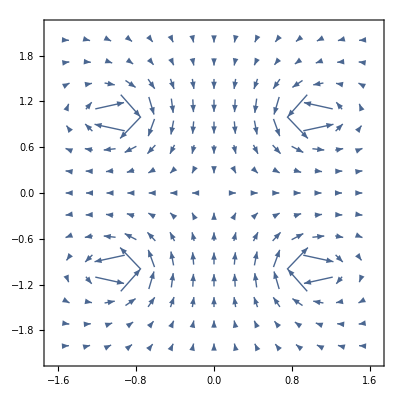

```mathematica
R =1; β=0; x0=0; z0=1;
VectorPlot[loopField[x,z,R,x0,z0,1,β]+loopField[x,z,R,-x0,-z0,-1,β],{x,-1.5,1.5},{z,-2,2}]
```

```mathematica
R =1; x0=0; z0=2.5; (*Coil radius, default x offset, and distance from center of cell*)
antiHHCoil[x_,z_,β_]:=loopField[x,z,R,x0,z0,1,β]+loopField[x,z,R,x0,-z0,-1,β];
shimCoil[x_,z_,β_]:=loopField[x,z,R,x0,z0,1,β]+loopField[x,z,R,x0,-z0,-1,β];
```

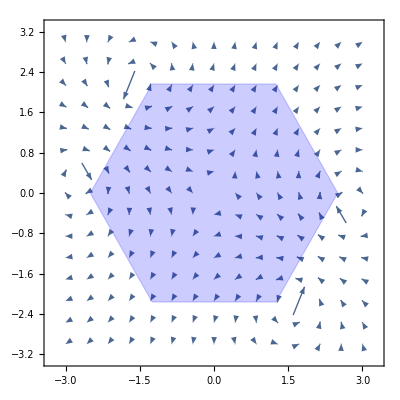

```mathematica
β = π/3;
Show[VectorPlot[antiHHCoil[x,z,β]+0*(shimCoil[x,z,0]+shimCoil[x,z,π/2]),{x,-3,3},{z,-3,3}],Graphics[{EdgeForm[Thick],Blue,Opacity[0.2],Polygon[Table[z0*{Cos[(n π)/3],Sin[(n π)/3]},{n,0,5}]]}]]
```

#### Appendixy Section: How to rotate a vector field in its plane

```mathematica
Ry[-π/4].{x,y}
Ry[π/4].{0,ⅇ^(-x^2)}
```

{x/(√2)+y/(√2),-x/(√2)+y/(√2)}

{-(ⅇ^(-x^2))/(√2),(ⅇ^(-x^2))/(√2)}

To rotate the whole field by β,  about the perpendicular to and intersecting the plot at (0,0), the vectors themselves must be rotated by β about their parallel axes, and the coordinate system rotated -β.

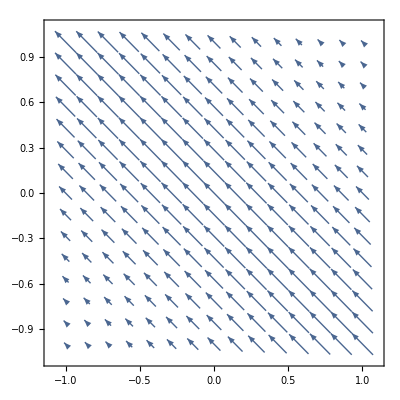

```mathematica
VectorPlot[{-(ⅇ^(-(x/(√2)+y/(√2))^2))/(√2),(ⅇ^(-(x/(√2)+y/(√2))^2))/(√2)},{x,-1,1},{y,-1,1}]
```